```mathematica
ClearAll[dirname, filename, data, data2]
```

d+1/2 ((2 eta^2 (n+1) omega t sin(2 omega t)+cos(2 omega t))/(4 eta^4 (n+1)^2 omega^2 t^2+1)+1)

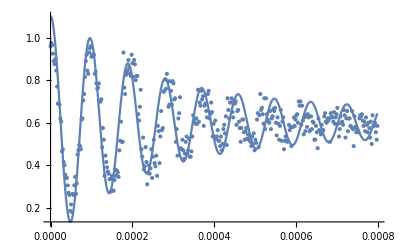

{omega→35603.5,n→7.23511,eta→0.146615,d→0.0946675}

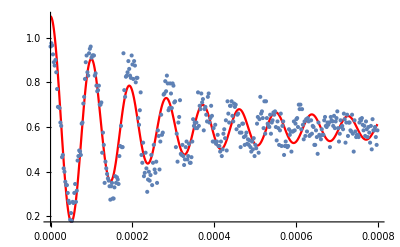

0.00566647

```mathematica
file = "D:\\Desktop\\Data\\Carrier_Before_Cooling.csv";
data = Import[file];
Dimensions[data];
data[[;;,1]]=data[[;;,1]]/10^6;
data[[;;,2]]=data[[;;,2]]/100;
data2 = data[[;;400,;;2]];

Clear[omega,n,t,eta,d];
expr = 1/2 (1+(Cos[2 omega t]+2 omega t eta^2(n+1)Sin[2 omega t])/(1+(2 omega t eta^2 (n+1))^2))+d;
TraditionalForm[expr]
xdata = Transpose[data2][[1]];
test = {omega->Pi/(88/10^6),n->10,eta->0.1,d->0.1};
Show[Plot[expr/.test,{t,Min[xdata],Max[xdata]},PlotRange->Full],ListPlot[data2,PlotRange->Full]]
fitresult = FindFit[data2,expr,{{omega,Pi/(88/10^6)},{n,10},{eta,0.1},{d,0.1}},t,MaxIterations->10000]
Show[Plot[expr/.fitresult,{t,Min[xdata],Max[xdata]},PlotRange->Full,PlotStyle->Red],ListPlot[data2,PlotRange->Full]]
omega/(2*Pi)/10^6/.fitresult
```